LabelStyle→Directive[20]

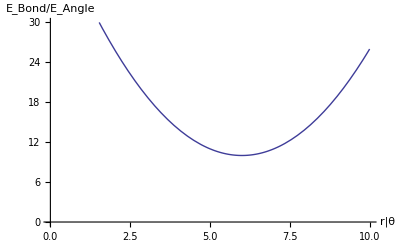

```mathematica
Plot[1*(r-6)^2+10,{r,0,10},PlotRange->{0,30},AxesLabel->{Style["r"|"θ",30],Style["E_Bond/E_Angle",25]},LabelStyle->Directive[0]]
```

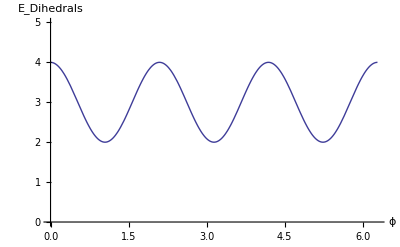

```mathematica
Plot[(1-Cos[3r+Pi])+2,{r,0,2*Pi},PlotRange->{0,5},AxesLabel->{Style["ϕ",30],Style["E_Dihedrals",30]},LabelStyle->Directive[0]]
```

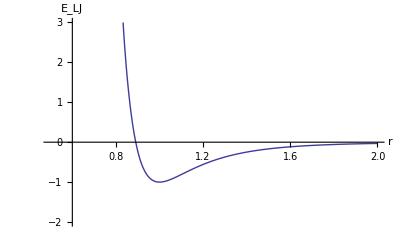

```mathematica
Plot[-2(1/r)^6+(1/r)^12,{r,.5,2},PlotRange->{-2,3},AxesLabel->{Style["r",30],Style["E_LJ",30]},LabelStyle->Directive[0]]
```

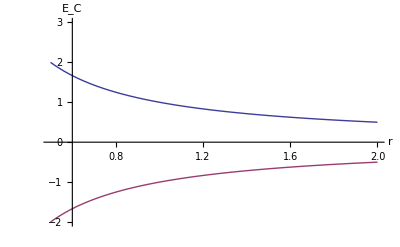

```mathematica
Plot[{(1/r),(-1/r)},{r,.5,2},PlotRange->{-2,3},AxesLabel->{Style["r",30],Style["E_C",30]},LabelStyle->Directive[0]]
```

```mathematica
Rotation Frequency Computations
```

```mathematica
per second
```

```mathematica
10^13*Exp[-3/.5]
```

2.47875×10^10

```mathematica
Exp[-3/.5]
```

0.00247875

LabelStyle→Directive[20]

Force Field Specific

```mathematica
The bonded constants present in the polyalkanes, polyethers and polysilicones are:
```

```mathematica
O
```

```mathematica
C
```

```mathematica
H
```

```mathematica
Si
```

```mathematica
The angular constants for simmilar systems are:
```

```mathematica
O
```

```mathematica
H
```

```mathematica
C
```

```mathematica
Si
```

```mathematica
Plot[1*(r-6)^2+10,{r,0,10},PlotRange->{0,30},AxesLabel->{Style["r"|"θ",30],Style["E_Bond/E_Angle",25]},LabelStyle->Directive[0]]
```

-Graphics-

```mathematica
The dihedral interaction constants are:
```

```mathematica
Plot[(1-Cos[3r+Pi])+2,{r,0,2*Pi},PlotRange->{0,5},AxesLabel->{Style["ϕ",30],Style["E_Dihedrals",30]},LabelStyle->Directive[0]]
```

-Graphics-

```mathematica
The Leonard Jones constants are:
```

```mathematica
Plot[-2(1/r)^6+(1/r)^12,{r,.5,2},PlotRange->{-2,3},AxesLabel->{Style["r",30],Style["E_LJ",30]},LabelStyle->Directive[0]]
```

-Graphics-

```mathematica
The Coulombic constants are:
```

```mathematica
Plot[{(1/r),(-1/r)},{r,.5,2},PlotRange->{-2,3},AxesLabel->{Style["r",30],Style["E_C",30]},LabelStyle->Directive[0]]
```

-Graphics-

```mathematica
The sum of the Leonard-Jones constants and the coulombic constants are:
```

Testing Dihedral Functions

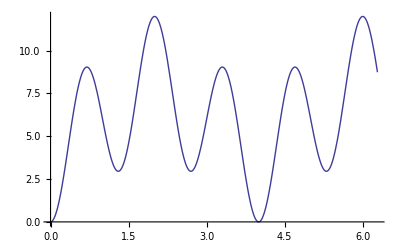

```mathematica
Plot[4(1-Cos[t*1.5Pi])+2(1-Cos[t*Pi/2]),{t,0,2Pi}]
```

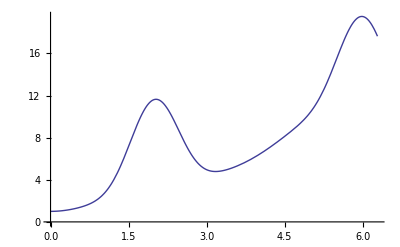

```mathematica
Plot[.5(1-Cos[t*Pi/2])^4+1(1-Cos[t*Pi/6])^3+.5(1-Cos[t*Pi/4])^2+1(1-Cos[t*Pi/2])+1,{t,0,2Pi}]
```

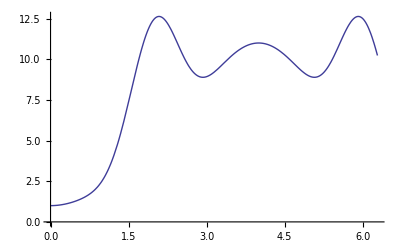

```mathematica
Plot[.5(1-Cos[t*Pi/2])^4+1(1-Cos[t*Pi/4])^3+.5(1-Cos[t*Pi/4])^2+1(1-Cos[t*Pi/2])+1,{t,0,2Pi}]
```

```mathematica
Mass vs. Number of Molecules for Presentation
```

```mathematica
Guy F. Mongelli
```

```mathematica
The purpose of this notebook is to determine the weight percent alcohol for various number of molecules of of alcohol at a constant total number of molecules.
```

```mathematica
The total number of molecules is 2783.  β represents the number of molecules of water.  α represents the number of molecules of the alcohol in the relevant system.
```

```mathematica
β=2783-α;
```

```mathematica
The molecular weights of alcohol and water respectively are:
```

```mathematica
xEtOH=46 (* g/mol *);
```

```mathematica
xMeOH=32 (* g/mol *);
```

```mathematica
xPOH=60.1 (* g/mol *);
```

```mathematica
xLOH (*Lauryl Alcohol*)=186.24(* g/mol *);
```

```mathematica
y=18 (* g/mol *);
```

```mathematica
MassPerEt[α_]=(α*xEtOH)/(α*xEtOH+(β)*y)
```

(46 α)/(18 (2783-α)+46 α)

```mathematica
MassPerMe[α_]=(α*xMeOH)/(α*xMeOH+(β)*y)
```

(32 α)/(18 (2783-α)+32 α)

```mathematica
MassPerP[α_]=(α*xPOH)/(α*xPOH+(β)*y)
```

(60.1 α)/(18 (2783-α)+60.1 α)

```mathematica
MassPerL[α_]=(α*xLOH)/(α*xLOH+(β)*y)
```

(186.24 α)/(18 (2783-α)+186.24 α)

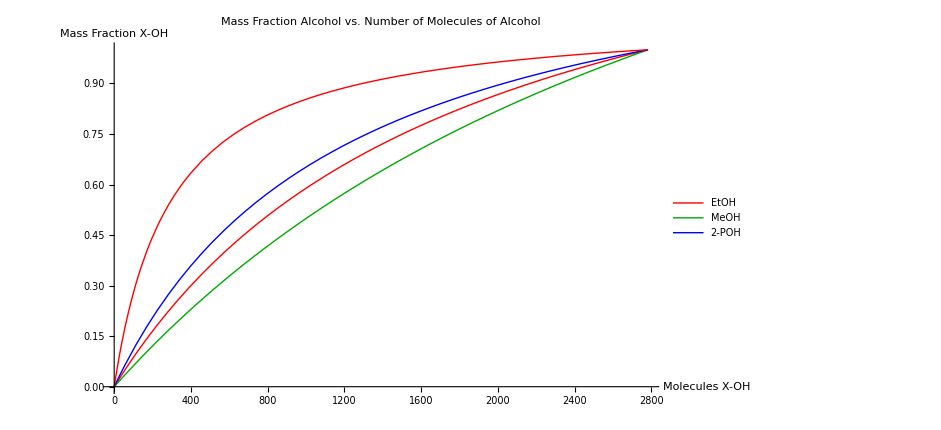

```mathematica
Plot[{MassPerEt[α],MassPerMe[α],MassPerP[α],MassPerL[α]},{α,0,2782},AxesLabel->{Style["Molecules X-OH",24],Style["Mass Fraction X-OH",24]},PlotLegends->{Style["EtOH",24],Style["MeOH",24],Style["2-POH",24]},PlotLabel->Style["Mass Fraction Alcohol vs. Number of Molecules of Alcohol",24],BaseStyle->{FontWeight->"Bold",FontSize->24},PlotStyle->{Red,Darker[Green],Blue}]
```

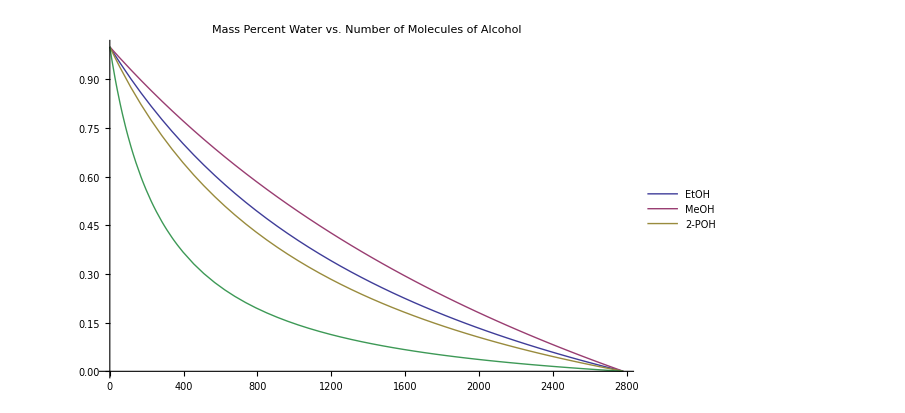

```mathematica
Plot[{1-MassPerEt[α],1-MassPerMe[α],1-MassPerP[α],1-MassPerL[α]},{α,0,2782},AxesLabel->Automatic,PlotLegends->{Style["EtOH",24],Style["MeOH",24],Style["2-POH",24]},PlotLabel->Style["Mass Percent Water vs. Number of Molecules of Alcohol",24],BaseStyle->{FontWeight->"Bold",FontSize->24}]
```

```mathematica
Solve[MassPerEt[α]==a,α]
```

{{α→-(25047 a)/(-23+14 a)}}

```mathematica
Solve[MassPerMe[α]==a,α]
```

{{α→-(25047 a)/(-16+7 a)}}

```mathematica
Solve[MassPerP[α]==a,α]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→-(500940. a)/(-601.+421. a)}}

```mathematica
Solve[MassPerL[α]==a,α]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→-(208725. a)/(-776.+701. a)}}

```mathematica
αEt[a_]=-(25047 a)/(-23+14 a);
```

```mathematica
αMe[a_]=-(25047 a)/(-16+7 a);
```

```mathematica
αP[a_]=-(500940. a)/(-601.+421. a);
```

```mathematica
αL[a_]=-(208725. a)/(-776.+701. a);
```

```mathematica
coeffs[a_]={a,Ceiling[N[αEt[a],4]],Ceiling[N[αMe[a],4]],Ceiling[N[αP[a],4]],Ceiling[N[αL[a],4]]}
```

{a,Ceiling[-(25050. a)/(-23.+14. a)],Ceiling[-(25050. a)/(-16.+7. a)],Ceiling[-(500940. a)/(-601.+421. a)],Ceiling[-(208725. a)/(-776.+701. a)]}

```mathematica
TableForm[Table[coeffs[a],{a,0,1,.10}],TableHeadings->{{},{"Mass Fraction X-OH","Molecules EtOH","Molecules MeOH","Molecules 2-POH","Molecules LOH"}}]
```

| Mass Fraction X-OH | Molecules EtOH | Molecules MeOH | Molecules 2-POH | Molecules LOH
 | 0. | 0 | 0 | 0 | 0
 | 0.1 | 116 | 164 | 90 | 30
 | 0.2 | 248 | 344 | 194 | 66
 | 0.3 | 400 | 541 | 317 | 111
 | 0.4 | 576 | 760 | 464 | 169
 | 0.5 | 783 | 1002 | 642 | 246
 | 0.6 | 1030 | 1274 | 863 | 353
 | 0.7 | 1329 | 1580 | 1145 | 513
 | 0.8 | 1699 | 1927 | 1517 | 776
 | 0.9 | 2168 | 2324 | 2030 | 1295
 | 1. | 2783 | 2783 | 2783 | 2783

```mathematica
Export["alcohols.txt",{{, "Mass Fraction X-OH", "Molecules EtOH", "Molecules MeOH", "Molecules 2-POH"}, {"", 0., 0, 0, 0}, {"", 0.1, 116, 164, 90}, {"", 0.2, 248, 344, 194}, {"", 0.3, 400, 541, 317}, {"", 0.4, 576, 760, 464}, {"", 0.5, 783, 1002, 642}, {"", 0.6, 1030, 1274, 863}, {"", 0.7, 1329, 1580, 1145}, {"", 0.8, 1699, 1927, 1517}, {"", 0.9, 2168, 2324, 2030}, {"", 1., 2783, 2783, 2783}}]
```

alcohols.txt

```mathematica
N[αEt[0]]
```

0.

```mathematica
coeffs2[a_]={a,Floor[2783-αEt[a]],Floor[2783-N[αMe[a],4]],Floor[N[2783-αP[a],4]],Floor[N[2783-αL[a],4]]}
```

{a,2783+Floor[(25047 a)/(-23+14 a)],2783+Floor[(25050. a)/(-16.+7. a)],Floor[2783.+(500940. a)/(-601.+421. a)],Floor[2783.+(208725. a)/(-776.+701. a)]}

```mathematica
TableForm[Table[coeffs2[a],{a,0,1,.10}],TableHeadings->{{},{"Mass Fraction X-OH","Molecules HOH (EtOH)","Molecules HOH (MeOH)","Molecules HOH (2-POH)","Molecules HOH (LOH)"}}]
```

| Mass Fraction X-OH | Molecules HOH (EtOH) | Molecules HOH (MeOH) | Molecules HOH (2-POH) | Molecules HOH (LOH)
 | 0. | 2783 | 2783 | 2783 | 2783
 | 0.1 | 2667 | 2619 | 2693 | 2753
 | 0.2 | 2535 | 2439 | 2589 | 2717
 | 0.3 | 2383 | 2242 | 2466 | 2672
 | 0.4 | 2207 | 2023 | 2319 | 2614
 | 0.5 | 2000 | 1781 | 2141 | 2537
 | 0.6 | 1753 | 1509 | 1920 | 2430
 | 0.7 | 1454 | 1203 | 1638 | 2270
 | 0.8 | 1084 | 856 | 1266 | 2007
 | 0.9 | 615 | 459 | 753 | 1488
 | 1. | 0 | 0 | 0 | 0

```mathematica
Export["aq.xlsx",{{"Mass Fraction X-OH", "Molecules HOH (EtOH)", "Molecules HOH (MeOH)", "Molecules HOH (2-POH)"}, {0., 2780, 2783, 2783}, {0.1, 2664, 2619, 2693}, {0.2, 2532, 2439, 2589}, {0.30000000000000004, 2380, 2242, 2466}, {0.4, 2204, 2023, 2319}, {0.5, 2000, 1781, 2141}, {0.6000000000000001, 1752, 1509, 1920}, {0.7000000000000001, 1452, 1203, 1638}, {0.8, 1084, 856, 1266}, {0.9, 612, 459, 753}, {1., 0, 0, 0}}]
```

$Failed

```mathematica
Guy F. Mongelli
```

```mathematica
The purpose of this notebook is to determine the weight percent alcohol for various number of molecules of of alcohol at a constant total number of molecules.
```

```mathematica
β=2783-α;
```

```mathematica
The molecular weights of alcohol and water respectively are:
```

```mathematica
xEtOH=46 (* g/mol *);
```

```mathematica
xMeOH=32 (* g/mol *);
```

```mathematica
xPOH=60.1 (* g/mol *);
```

```mathematica
y=18 (* g/mol *);
```

```mathematica
MassPerEt[α_]=(α*xEtOH)/(α*xEtOH+(β)*y)
```

(46 α)/(46 α+18 β)

```mathematica
MassPerMe[α_]=(α*xMeOH)/(α*xMeOH+(β)*y)
```

(32 α)/(32 α+18 β)

```mathematica
MassPerP[α_]=(α*xPOH)/(α*xPOH+(β)*y)
```

(60.1 α)/(60.1 α+18 β)

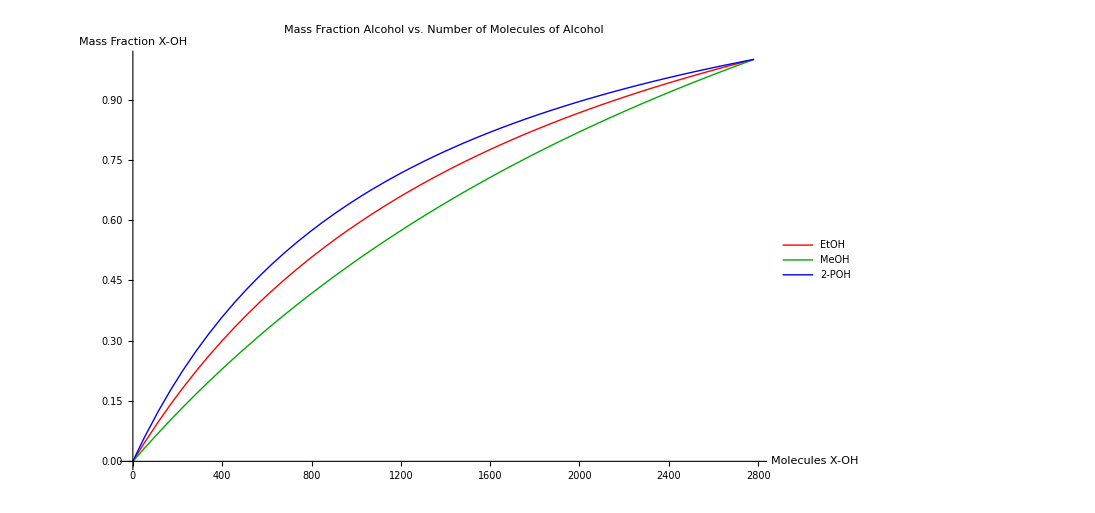

```mathematica
Plot[{MassPerEt[α],MassPerMe[α],MassPerP[α]},{α,0,2782},AxesLabel->{Style["Molecules X-OH",24],Style["Mass Fraction X-OH",24]},PlotLegends->{Style["EtOH",24],Style["MeOH",24],Style["2-POH",24]},PlotLabel->Style["Mass Fraction Alcohol vs. Number of Molecules of Alcohol",24],BaseStyle->{FontWeight->"Bold",FontSize->24},PlotStyle->{Red,Darker[Green],Blue}]
```

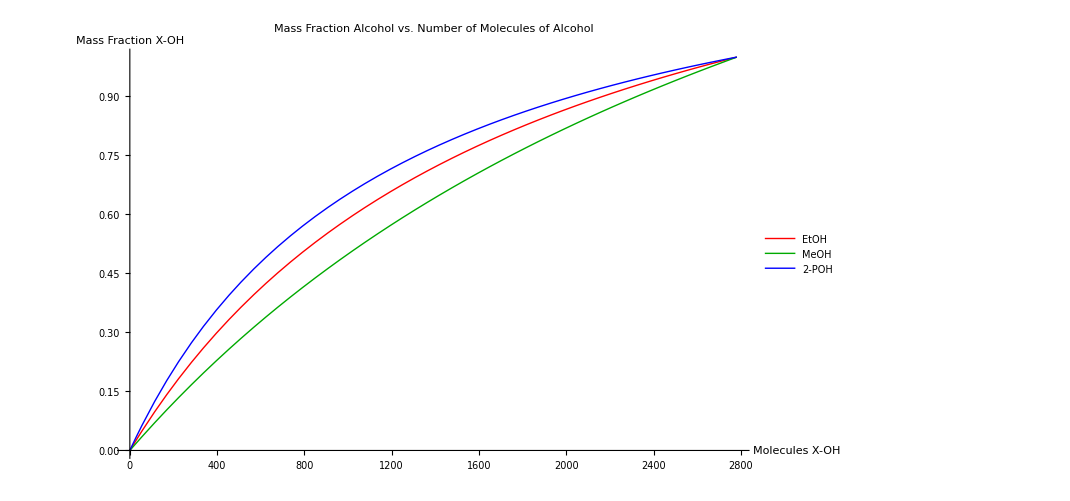
```mathematica
Export["graph.jpeg",-Graphics-]
```

graph.jpeg

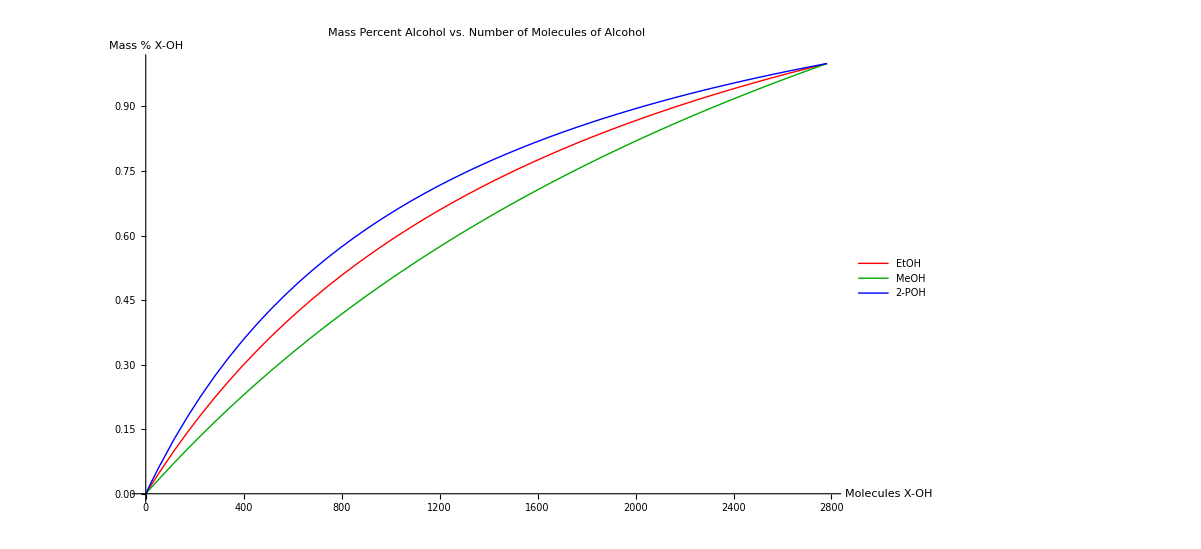
```mathematica
Export["graph.jpeg",-Graphics-]
```

graph.jpeg

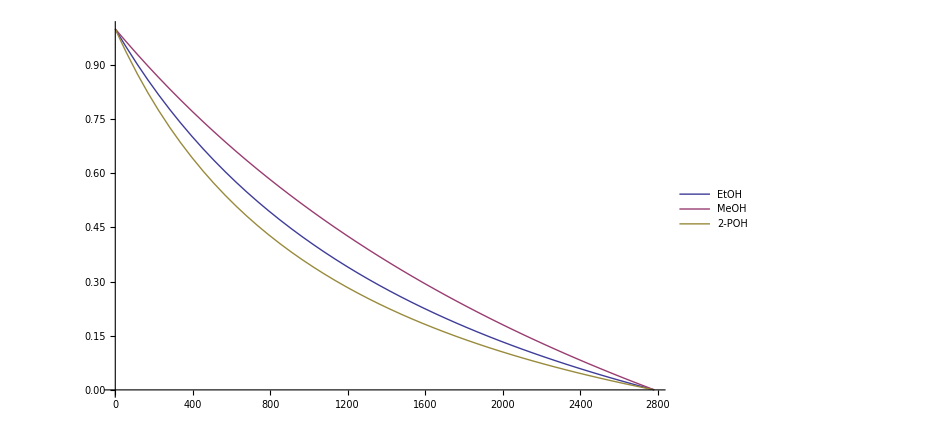

```mathematica
Plot[{1-MassPerEt[α],1-MassPerMe[α],1-MassPerP[α]},{α,0,2782},AxesLabel->Automatic,PlotLegends->{"EtOH","MeOH","2-POH"},PlotLabel->{"Mass Percent Water vs. Number of Molecules of Alcohol"}]
```

```mathematica
Clear[β]
```

```mathematica
Solve[(α*xXOH)/(α*xXOH+(β)*y)==a,α]
```

{{α→-(50094 a)/(-18 a-xXOH+a xXOH)}}

```mathematica
Solve[MassPerEt[α]==a,α]
```

{{α→-(25047 a)/(-23+14 a)}}

```mathematica
Solve[MassPerMe[α]==a,α]
```

{{α→-(25047 a)/(-16+7 a)}}

```mathematica
Solve[MassPerP[α]==a,α]
```

{{α→-(500940. a)/(-601.+421. a)}}

```mathematica
αEt[a_]=-(25047 a)/(-23+14 a);
```

```mathematica
αMe[a_]=-(25047 a)/(-16+7 a);
```

```mathematica
αP[a_]=-(500940. a)/(-601.+421. a);
```

```mathematica
coeffs[a_]={a,Ceiling[N[αEt[a],4]],Ceiling[N[αMe[a],4]],Ceiling[N[αP[a],4]]}
```

{a,Ceiling[-(25050. a)/(-23.+14. a)],Ceiling[-(25050. a)/(-16.+7. a)],Ceiling[-(500940. a)/(-601.+421. a)]}

```mathematica
TableForm[Table[coeffs[a],{a,0,1,.10}],TableHeadings->{{},{"Mass Fraction X-OH","Molecules EtOH","Molecules MeOH","Molecules 2-POH"}}]
```

| Mass Fraction X-OH | Molecules EtOH | Molecules MeOH | Molecules 2-POH
 | 0. | 0 | 0 | 0
 | 0.1 | 116 | 164 | 90
 | 0.2 | 248 | 344 | 194
 | 0.3 | 400 | 541 | 317
 | 0.4 | 576 | 760 | 464
 | 0.5 | 783 | 1002 | 642
 | 0.6 | 1030 | 1274 | 863
 | 0.7 | 1329 | 1580 | 1145
 | 0.8 | 1699 | 1927 | 1517
 | 0.9 | 2168 | 2324 | 2030
 | 1. | 2783 | 2783 | 2783

```mathematica
Export["alcohols.txt",{{, "Mass Fraction X-OH", "Molecules EtOH", "Molecules MeOH", "Molecules 2-POH"}, {"", 0., 0, 0, 0}, {"", 0.1, 116, 164, 90}, {"", 0.2, 248, 344, 194}, {"", 0.3, 400, 541, 317}, {"", 0.4, 576, 760, 464}, {"", 0.5, 783, 1002, 642}, {"", 0.6, 1030, 1274, 863}, {"", 0.7, 1329, 1580, 1145}, {"", 0.8, 1699, 1927, 1517}, {"", 0.9, 2168, 2324, 2030}, {"", 1., 2783, 2783, 2783}}]
```

alcohols.txt

```mathematica
N[αEt[0]]
```

0.

```mathematica
coeffs2[a_]={a,Floor[2783-αEt[a]],Floor[2783-N[αMe[a],4]],Floor[N[2783-αP[a],4]]}
```

{a,2783+Floor[(25047 a)/(-23+14 a)],2783+Floor[(25050. a)/(-16.+7. a)],Floor[2783.+(500940. a)/(-601.+421. a)]}

```mathematica
TableForm[Table[coeffs2[a],{a,0,1,.10}],TableHeadings->{{},{"Mass Fraction X-OH","Molecules HOH (EtOH)","Molecules HOH (MeOH)","Molecules HOH (2-POH)"}}]
```

| Mass Fraction X-OH | Molecules HOH (EtOH) | Molecules HOH (MeOH) | Molecules HOH (2-POH)
 | 0. | 2783 | 2783 | 2783
 | 0.1 | 2667 | 2619 | 2693
 | 0.2 | 2535 | 2439 | 2589
 | 0.3 | 2383 | 2242 | 2466
 | 0.4 | 2207 | 2023 | 2319
 | 0.5 | 2000 | 1781 | 2141
 | 0.6 | 1753 | 1509 | 1920
 | 0.7 | 1454 | 1203 | 1638
 | 0.8 | 1084 | 856 | 1266
 | 0.9 | 615 | 459 | 753
 | 1. | 0 | 0 | 0

```mathematica
Export["aq.xlsx",{{"Mass Fraction X-OH", "Molecules HOH (EtOH)", "Molecules HOH (MeOH)", "Molecules HOH (2-POH)"}, {0., 2780, 2783, 2783}, {0.1, 2664, 2619, 2693}, {0.2, 2532, 2439, 2589}, {0.30000000000000004, 2380, 2242, 2466}, {0.4, 2204, 2023, 2319}, {0.5, 2000, 1781, 2141}, {0.6000000000000001, 1752, 1509, 1920}, {0.7000000000000001, 1452, 1203, 1638}, {0.8, 1084, 856, 1266}, {0.9, 612, 459, 753}, {1., 0, 0, 0}}]
```

$Failed

```mathematica
Guy F. Mongelli
```

```mathematica
The purpose of this notebook is to determine the weight percent alcohol for various number of molecules of of alcohol at a constant total number of molecules.
```

```mathematica
The total number of molecules is 2783.  β represents the number of molecules of water.  α represents the number of molecules of the alcohol in the relevant system.
```

```mathematica
β=2783-α;
```

```mathematica
The molecular weights of alcohol and water respectively are:
```

```mathematica
xEtOH=46 (* g/mol *);
```

```mathematica
xMeOH=32 (* g/mol *);
```

```mathematica
xPOH=60.1 (* g/mol *);
```

```mathematica
xLOH (*Lauryl Alcohol*)=186.24(* g/mol *);
```

```mathematica
y=18 (* g/mol *);
```

```mathematica
MassPerEt[α_]=(α*xEtOH)/(α*xEtOH+(β)*y)
```

(46 α)/(18 (2783-α)+46 α)

```mathematica
MassPerMe[α_]=(α*xMeOH)/(α*xMeOH+(β)*y)
```

(32 α)/(18 (2783-α)+32 α)

```mathematica
MassPerP[α_]=(α*xPOH)/(α*xPOH+(β)*y)
```

(60.1 α)/(18 (2783-α)+60.1 α)

```mathematica
MassPerL[α_]=(α*xLOH)/(α*xLOH+(β)*y)
```

(186.24 α)/(18 (2783-α)+186.24 α)

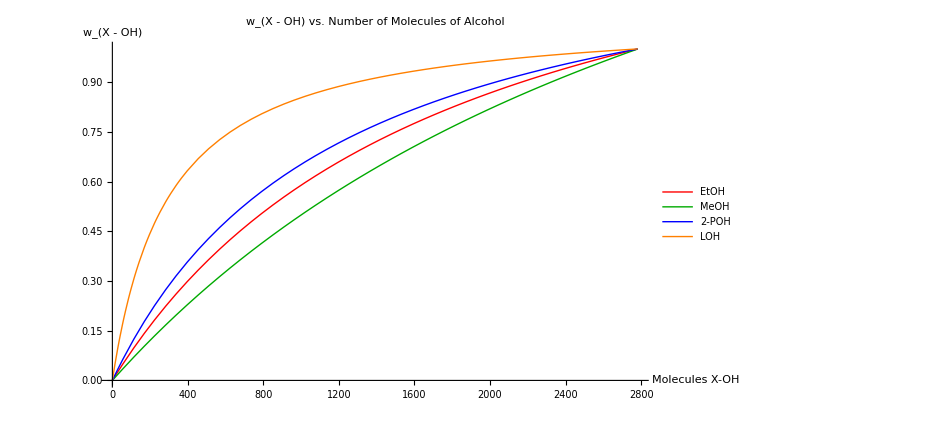

```mathematica
Plot[{MassPerEt[α],MassPerMe[α],MassPerP[α],MassPerL[α]},{α,0,2782},AxesLabel->{Style["Molecules X-OH",24],Style["w_(X - OH)",24]},PlotLegends->{Style["EtOH",24],Style["MeOH",24],Style["2-POH",24],Style["LOH",24]},PlotLabel->Style["w_(X - OH) vs. Number of Molecules of Alcohol",24],BaseStyle->{FontWeight->"Bold",FontSize->24},PlotStyle->{Red,Darker[Green],Blue,Orange}]
```

```mathematica
Export["graph_7.13.2013.jpeg",-Graphics-]
```

graph_7.13.2013.jpeg

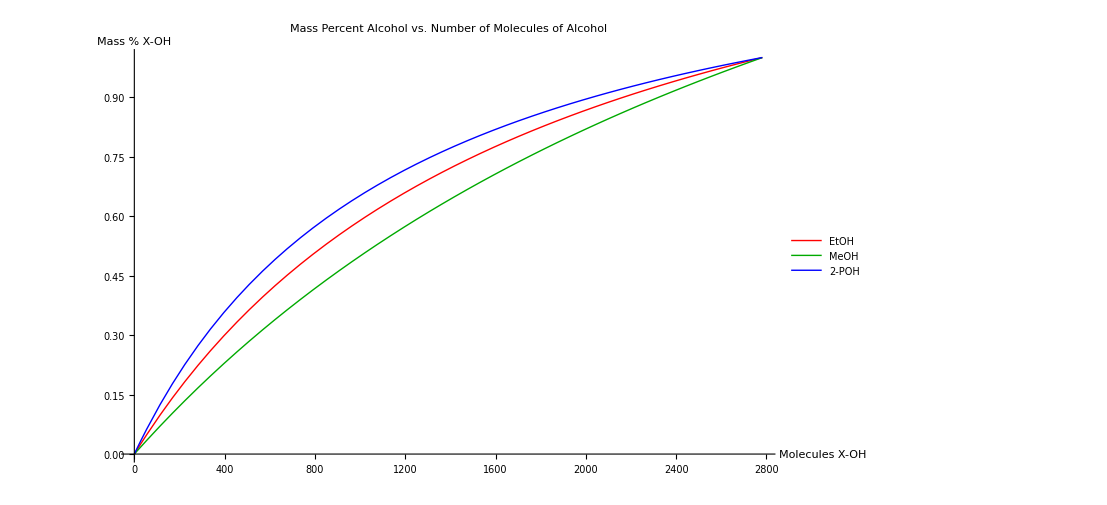
```mathematica
Export["graph.jpeg",-Graphics-]
```

graph.jpeg

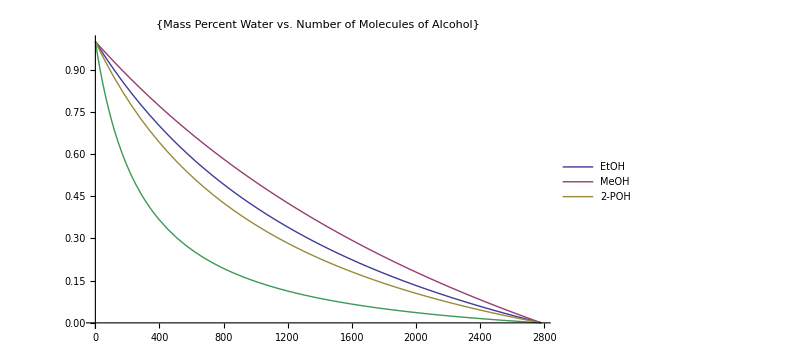

```mathematica
Plot[{1-MassPerEt[α],1-MassPerMe[α],1-MassPerP[α],1-MassPerL[α]},{α,0,2782},AxesLabel->Automatic,PlotLegends->{"EtOH","MeOH","2-POH"},PlotLabel->{"Mass Percent Water vs. Number of Molecules of Alcohol"}]
```

```mathematica
Solve[MassPerEt[α]==a,α]
```

{{α→-(25047 a)/(-23+14 a)}}

```mathematica
Solve[MassPerMe[α]==a,α]
```

{{α→-(25047 a)/(-16+7 a)}}

```mathematica
Solve[MassPerP[α]==a,α]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→-(500940. a)/(-601.+421. a)}}

```mathematica
Solve[MassPerL[α]==a,α]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→-(208725. a)/(-776.+701. a)}}

```mathematica
αEt[a_]=-(25047 a)/(-23+14 a);
```

```mathematica
αMe[a_]=-(25047 a)/(-16+7 a);
```

```mathematica
αP[a_]=-(500940. a)/(-601.+421. a);
```

```mathematica
αL[a_]=-(208725. a)/(-776.+701. a);
```

```mathematica
coeffs[a_]={a,Ceiling[N[αEt[a],4]],Ceiling[N[αMe[a],4]],Ceiling[N[αP[a],4]],Ceiling[N[αL[a],4]]}
```

{a,Ceiling[-(25050. a)/(-23.+14. a)],Ceiling[-(25050. a)/(-16.+7. a)],Ceiling[-(500940. a)/(-601.+421. a)],Ceiling[-(208725. a)/(-776.+701. a)]}

```mathematica
TableForm[Table[coeffs[a],{a,0,1,.10}],TableHeadings->{{},{"Mass Fraction X-OH","Molecules EtOH","Molecules MeOH","Molecules 2-POH","Molecules LOH"}}]
```

| Mass Fraction X-OH | Molecules EtOH | Molecules MeOH | Molecules 2-POH | Molecules LOH
 | 0. | 0 | 0 | 0 | 0
 | 0.1 | 116 | 164 | 90 | 30
 | 0.2 | 248 | 344 | 194 | 66
 | 0.3 | 400 | 541 | 317 | 111
 | 0.4 | 576 | 760 | 464 | 169
 | 0.5 | 783 | 1002 | 642 | 246
 | 0.6 | 1030 | 1274 | 863 | 353
 | 0.7 | 1329 | 1580 | 1145 | 513
 | 0.8 | 1699 | 1927 | 1517 | 776
 | 0.9 | 2168 | 2324 | 2030 | 1295
 | 1. | 2783 | 2783 | 2783 | 2783

```mathematica
Export["alcohols.txt",{{, "Mass Fraction X-OH", "Molecules EtOH", "Molecules MeOH", "Molecules 2-POH"}, {"", 0., 0, 0, 0}, {"", 0.1, 116, 164, 90}, {"", 0.2, 248, 344, 194}, {"", 0.3, 400, 541, 317}, {"", 0.4, 576, 760, 464}, {"", 0.5, 783, 1002, 642}, {"", 0.6, 1030, 1274, 863}, {"", 0.7, 1329, 1580, 1145}, {"", 0.8, 1699, 1927, 1517}, {"", 0.9, 2168, 2324, 2030}, {"", 1., 2783, 2783, 2783}}]
```

alcohols.txt

```mathematica
N[αEt[0]]
```

0.

```mathematica
coeffs2[a_]={a,Floor[2783-αEt[a]],Floor[2783-N[αMe[a],4]],Floor[N[2783-αP[a],4]],Floor[N[2783-αL[a],4]]}
```

{a,2783+Floor[(25047 a)/(-23+14 a)],2783+Floor[(25050. a)/(-16.+7. a)],Floor[2783.+(500940. a)/(-601.+421. a)],Floor[2783.+(208725. a)/(-776.+701. a)]}

```mathematica
TableForm[Table[coeffs2[a],{a,0,1,.10}],TableHeadings->{{},{"Mass Fraction X-OH","Molecules HOH (EtOH)","Molecules HOH (MeOH)","Molecules HOH (2-POH)","Molecules HOH (LOH)"}}]
```

| Mass Fraction X-OH | Molecules HOH (EtOH) | Molecules HOH (MeOH) | Molecules HOH (2-POH) | Molecules HOH (LOH)
 | 0. | 2783 | 2783 | 2783 | 2783
 | 0.1 | 2667 | 2619 | 2693 | 2753
 | 0.2 | 2535 | 2439 | 2589 | 2717
 | 0.3 | 2383 | 2242 | 2466 | 2672
 | 0.4 | 2207 | 2023 | 2319 | 2614
 | 0.5 | 2000 | 1781 | 2141 | 2537
 | 0.6 | 1753 | 1509 | 1920 | 2430
 | 0.7 | 1454 | 1203 | 1638 | 2270
 | 0.8 | 1084 | 856 | 1266 | 2007
 | 0.9 | 615 | 459 | 753 | 1488
 | 1. | 0 | 0 | 0 | 0

```mathematica
Export["aq.xlsx",{{"Mass Fraction X-OH", "Molecules HOH (EtOH)", "Molecules HOH (MeOH)", "Molecules HOH (2-POH)"}, {0., 2780, 2783, 2783}, {0.1, 2664, 2619, 2693}, {0.2, 2532, 2439, 2589}, {0.30000000000000004, 2380, 2242, 2466}, {0.4, 2204, 2023, 2319}, {0.5, 2000, 1781, 2141}, {0.6000000000000001, 1752, 1509, 1920}, {0.7000000000000001, 1452, 1203, 1638}, {0.8, 1084, 856, 1266}, {0.9, 612, 459, 753}, {1., 0, 0, 0}}]
```

$Failed

```mathematica
Guy F. Mongelli
```

```mathematica
The purpose of this notebook is to determine the weight percent alcohol for various number of molecules of of alcohol at a constant total number of molecules.
```

```mathematica
The total number of molecules is 2783.  β represents the number of molecules of water.  α represents the number of molecules of the alcohol in the relevant system.
```

```mathematica
β=2783-α;
```

```mathematica
The molecular weights of alcohol and water respectively are:
```

```mathematica
xEtOH=46 (* g/mol *);
```

```mathematica
xMeOH=32 (* g/mol *);
```

```mathematica
xPOH=60.1 (* g/mol *);
```

```mathematica
xLOH (*Lauryl Alcohol*)=186.24(* g/mol *);
```

```mathematica
xAMC(* acetyl methyl carbinol=acetoin *)= 88.11 (*g /mol*);
```

```mathematica
xDMK (*dimethyl ketone*)= 58.08 (* g/mol *);
```

```mathematica
y=18 (* g/mol *);
```

```mathematica
MassPerEt[α_]=(α*xEtOH)/(α*xEtOH+(β)*y)
```

(46 α)/(18 (2783-α)+46 α)

```mathematica
MassPerMe[α_]=(α*xMeOH)/(α*xMeOH+(β)*y)
```

(32 α)/(18 (2783-α)+32 α)

```mathematica
MassPerP[α_]=(α*xPOH)/(α*xPOH+(β)*y)
```

(60.1 α)/(18 (2783-α)+60.1 α)

```mathematica
MassPerL[α_]=(α*xLOH)/(α*xLOH+(β)*y)
```

(186.24 α)/(18 (2783-α)+186.24 α)

```mathematica
MassPerA[α_]=(α*xAMC)/(α*xAMC+(β)*y)
```

(88.11 α)/(18 (2783-α)+88.11 α)

```mathematica
MassPerD[α_]=(α*xDMK)/(α*xDMK+(β)*y)
```

(58.08 α)/(18 (2783-α)+58.08 α)

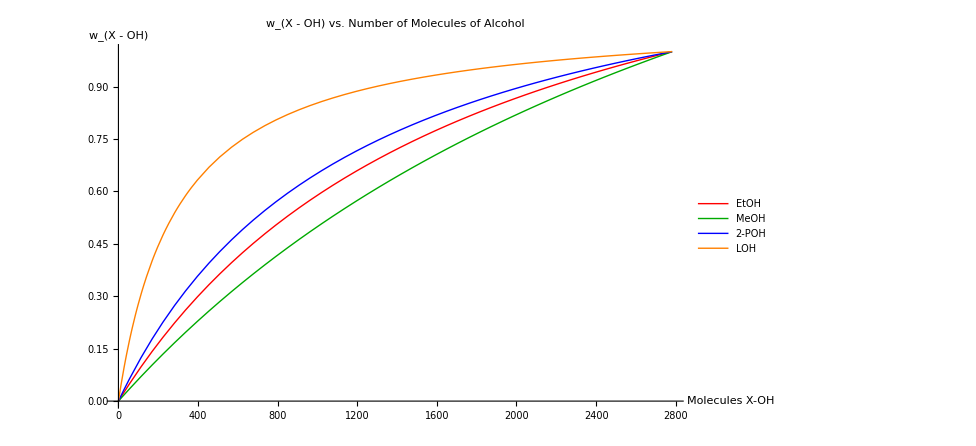

```mathematica
Plot[{MassPerEt[α],MassPerMe[α],MassPerP[α],MassPerL[α]},{α,0,2782},AxesLabel->{Style["Molecules X-OH",24],Style["w_(X - OH)",24]},PlotLegends->{Style["EtOH",24],Style["MeOH",24],Style["2-POH",24],Style["LOH",24]},PlotLabel->Style["w_(X - OH) vs. Number of Molecules of Alcohol",24],BaseStyle->{FontWeight->"Bold",FontSize->24},PlotStyle->{Red,Darker[Green],Blue,Orange}]
```

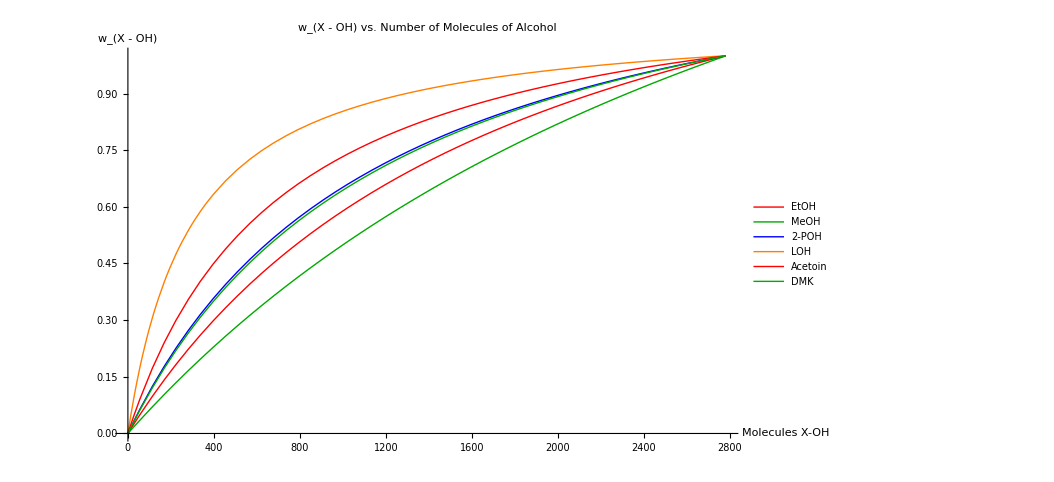

```mathematica
Plot[{MassPerEt[α],MassPerMe[α],MassPerP[α],MassPerL[α],MassPerA[α],MassPerD[α]},{α,0,2782},AxesLabel->{Style["Molecules X-OH",24],Style["w_(X - OH)",24]},PlotLegends->{Style["EtOH",24],Style["MeOH",24],Style["2-POH",24],Style["LOH",24],Style["Acetoin",24],Style["DMK",24]},PlotLabel->Style["w_(X - OH) vs. Number of Molecules of Alcohol",24],BaseStyle->{FontWeight->"Bold",FontSize->24},PlotStyle->{Red,Darker[Green],Blue,Orange}]
```

```mathematica
Export["graph_7.13.2013.jpeg",-Graphics-]
```

graph_7.13.2013.jpeg

```mathematica
Export["graph.jpeg",-Graphics-]
```

graph.jpeg

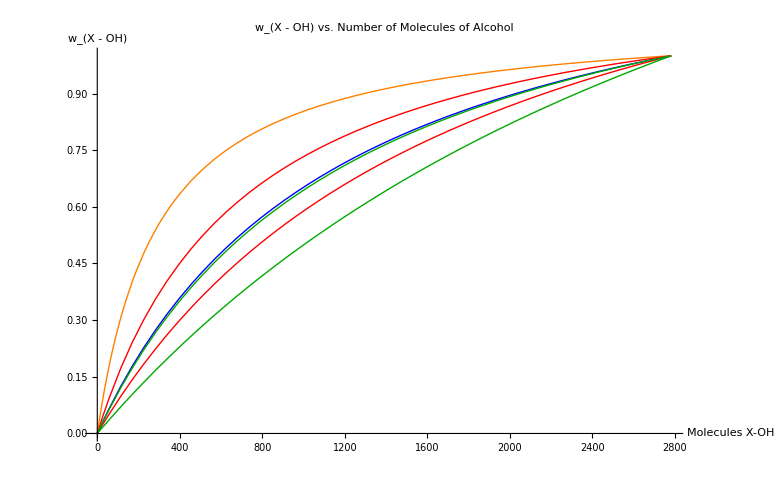
```mathematica
Export["graph_12.20.2013.jpeg",-Graphics-]
```

graph_12.20.2013.jpeg

```mathematica
Plot[{1-MassPerEt[α],1-MassPerMe[α],1-MassPerP[α],1-MassPerL[α]},{α,0,2782},AxesLabel->Automatic,PlotLegends->{"EtOH","MeOH","2-POH"},PlotLabel->{"Mass Percent Water vs. Number of Molecules of Alcohol"}]
```

-Graphics-

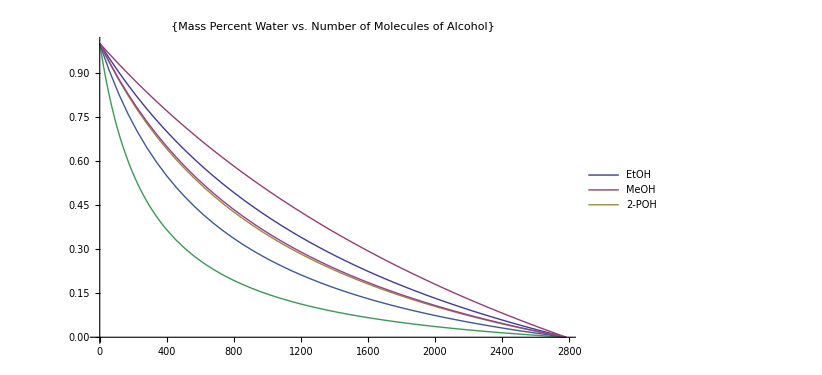

```mathematica
Plot[{1-MassPerEt[α],1-MassPerMe[α],1-MassPerP[α],1-MassPerL[α],1-MassPerA[α],1-MassPerD[α]},{α,0,2782},AxesLabel->Automatic,PlotLegends->{"EtOH","MeOH","2-POH"},PlotLabel->{"Mass Percent Water vs. Number of Molecules of Alcohol"}]
```

```mathematica
Solve[MassPerEt[α]==a,α]
```

{{α→-(25047 a)/(-23+14 a)}}

```mathematica
Solve[MassPerMe[α]==a,α]
```

{{α→-(25047 a)/(-16+7 a)}}

```mathematica
Solve[MassPerP[α]==a,α]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→-(500940. a)/(-601.+421. a)}}

```mathematica
Solve[MassPerL[α]==a,α]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→-(208725. a)/(-776.+701. a)}}

```mathematica
Solve[MassPerA[α]==a,α]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→-(556600. a)/(-979.+779. a)}}

```mathematica
Solve[MassPerD[α]==a,α]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→-(208725. a)/(-242.+167. a)}}

```mathematica
αEt[a_]=-(25047 a)/(-23+14 a);
```

```mathematica
αMe[a_]=-(25047 a)/(-16+7 a);
```

```mathematica
αP[a_]=-(500940. a)/(-601.+421. a);
```

```mathematica
αL[a_]=-(208725. a)/(-776.+701. a);
```

```mathematica
αA[a_]=-(556600. a)/(-979.+779. a);
```

```mathematica
αD[a_]=-(208725. a)/(-242.+167. a);
```

```mathematica
coeffs[a_]={a,Ceiling[N[αEt[a],4]],Ceiling[N[αMe[a],4]],Ceiling[N[αP[a],4]],Ceiling[N[αL[a],4]]}
```

{a,Ceiling[-(25050. a)/(-23.+14. a)],Ceiling[-(25050. a)/(-16.+7. a)],Ceiling[-(500940. a)/(-601.+421. a)],Ceiling[-(208725. a)/(-776.+701. a)]}

```mathematica
coeffs[a_]={a,Ceiling[N[αEt[a],4]],Ceiling[N[αMe[a],4]],Ceiling[N[αP[a],4]],Ceiling[N[αL[a],4]],Ceiling[N[αA[a],4]],Ceiling[N[αD[a],4]]}
```

{a,Ceiling[-(25050. a)/(-23.+14. a)],Ceiling[-(25050. a)/(-16.+7. a)],Ceiling[-(500940. a)/(-601.+421. a)],Ceiling[-(208725. a)/(-776.+701. a)],Ceiling[-(556600. a)/(-979.+779. a)],Ceiling[-(208725. a)/(-242.+167. a)]}

```mathematica
TableForm[Table[coeffs[a],{a,0,1,.10}],TableHeadings->{{},{"Mass Fraction X-OH","Molecules EtOH","Molecules MeOH","Molecules 2-POH","Molecules LOH","Molecules Acetoin","Molecules DMK"}}]
```

| Mass Fraction X-OH | Molecules EtOH | Molecules MeOH | Molecules 2-POH | Molecules LOH | Molecules Acetoin | Molecules DMK
 | 0. | 0 | 0 | 0 | 0 | 0 | 0
 | 0.1 | 116 | 164 | 90 | 30 | 62 | 93
 | 0.2 | 248 | 344 | 194 | 66 | 136 | 201
 | 0.3 | 400 | 541 | 317 | 111 | 225 | 327
 | 0.4 | 576 | 760 | 464 | 169 | 334 | 477
 | 0.5 | 783 | 1002 | 642 | 246 | 473 | 659
 | 0.6 | 1030 | 1274 | 863 | 353 | 653 | 884
 | 0.7 | 1329 | 1580 | 1145 | 513 | 899 | 1168
 | 0.8 | 1699 | 1927 | 1517 | 776 | 1252 | 1541
 | 0.9 | 2168 | 2324 | 2030 | 1295 | 1803 | 2049
 | 1. | 2783 | 2783 | 2783 | 2783 | 2783 | 2783

```mathematica
Export["alcohols.txt",{{, "Mass Fraction X-OH", "Molecules EtOH", "Molecules MeOH", "Molecules 2-POH"}, {"", 0., 0, 0, 0}, {"", 0.1, 116, 164, 90}, {"", 0.2, 248, 344, 194}, {"", 0.3, 400, 541, 317}, {"", 0.4, 576, 760, 464}, {"", 0.5, 783, 1002, 642}, {"", 0.6, 1030, 1274, 863}, {"", 0.7, 1329, 1580, 1145}, {"", 0.8, 1699, 1927, 1517}, {"", 0.9, 2168, 2324, 2030}, {"", 1., 2783, 2783, 2783}}]
```

```mathematica
Export["alcohols.txt",{{, "Mass Fraction X-OH", "Molecules EtOH", "Molecules MeOH", "Molecules 2-POH", "Molecules LOH", "Molecules Acetoin", "Molecules DMK"}, {"", 0., 0, 0, 0, 0, 0, 0}, {"", 0.1, 116, 164, 90, 30, 62, 93}, {"", 0.2, 248, 344, 194, 66, 136, 201}, {"", 0.30, 400, 541, 317, 111, 225, 327}, {"", 0.4, 576, 760, 464, 169, 334, 477}, {"", 0.5, 783, 1002, 642, 246, 473, 659}, {"", 0.60, 1030, 1274, 863, 353, 653, 884}, {"", 0.70, 1329, 1580, 1145, 513, 899, 1168}, {"", 0.8, 1699, 1927, 1517, 776, 1252, 1541}, {"", 0.9, 2168, 2324, 2030, 1295, 1803, 2049}, {"", 1., 2783, 2783, 2783, 2783, 2783, 2783}}]
```

alcohols.txt

```mathematica
N[αEt[0]]
```

0.

```mathematica
coeffs2[a_]={a,Floor[2783-αEt[a]],Floor[2783-N[αMe[a],4]],Floor[N[2783-αP[a],4]],Floor[N[2783-αL[a],4]]}
```

{a,2783+Floor[(25047 a)/(-23+14 a)],2783+Floor[(25050. a)/(-16.+7. a)],Floor[2783.+(500940. a)/(-601.+421. a)],Floor[2783.+(208725. a)/(-776.+701. a)]}

```mathematica
coeffs2[a_]={a,Floor[2783-αEt[a]],Floor[2783-N[αMe[a],4]],Floor[N[2783-αP[a],4]],Floor[N[2783-αL[a],4]],Floor[N[2783-αA[a],4]],Floor[N[2783-αD[a],4]]}
```

{a,2783+Floor[(25047 a)/(-23+14 a)],2783+Floor[(25050. a)/(-16.+7. a)],Floor[2783.+(500940. a)/(-601.+421. a)],Floor[2783.+(208725. a)/(-776.+701. a)],Floor[2783.+(556600. a)/(-979.+779. a)],Floor[2783.+(208725. a)/(-242.+167. a)]}

```mathematica
TableForm[Table[coeffs2[a],{a,0,1,.10}],TableHeadings->{{},{"Mass Fraction X-OH","Molecules HOH (EtOH)","Molecules HOH (MeOH)","Molecules HOH (2-POH)","Molecules HOH (LOH)"}}]
```

| Mass Fraction X-OH | Molecules HOH (EtOH) | Molecules HOH (MeOH) | Molecules HOH (2-POH) | Molecules HOH (LOH)
 | 0. | 2783 | 2783 | 2783 | 2783
 | 0.1 | 2667 | 2619 | 2693 | 2753
 | 0.2 | 2535 | 2439 | 2589 | 2717
 | 0.3 | 2383 | 2242 | 2466 | 2672
 | 0.4 | 2207 | 2023 | 2319 | 2614
 | 0.5 | 2000 | 1781 | 2141 | 2537
 | 0.6 | 1753 | 1509 | 1920 | 2430
 | 0.7 | 1454 | 1203 | 1638 | 2270
 | 0.8 | 1084 | 856 | 1266 | 2007
 | 0.9 | 615 | 459 | 753 | 1488
 | 1. | 0 | 0 | 0 | 0

```mathematica
TableForm[Table[coeffs2[a],{a,0,1,.10}],TableHeadings->{{},{"Mass Fraction X-OH","Molecules HOH (EtOH)","Molecules HOH (MeOH)","Molecules HOH (2-POH)","Molecules HOH (2-POH)","Molecules HOH (acetoin)","Molecules HOH (DMK)"}}]
```

| Mass Fraction X-OH | Molecules HOH (EtOH) | Molecules HOH (MeOH) | Molecules HOH (2-POH) | Molecules HOH (2-POH) | Molecules HOH (acetoin) | Molecules HOH (DMK)
 | 0. | 2783 | 2783 | 2783 | 2783 | 2783 | 2783
 | 0.1 | 2667 | 2619 | 2693 | 2753 | 2721 | 2690
 | 0.2 | 2535 | 2439 | 2589 | 2717 | 2647 | 2582
 | 0.3 | 2383 | 2242 | 2466 | 2672 | 2558 | 2456
 | 0.4 | 2207 | 2023 | 2319 | 2614 | 2449 | 2306
 | 0.5 | 2000 | 1781 | 2141 | 2537 | 2310 | 2124
 | 0.6 | 1753 | 1509 | 1920 | 2430 | 2130 | 1899
 | 0.7 | 1454 | 1203 | 1638 | 2270 | 1884 | 1615
 | 0.8 | 1084 | 856 | 1266 | 2007 | 1531 | 1242
 | 0.9 | 615 | 459 | 753 | 1488 | 980 | 734
 | 1. | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
Export["aq.xlsx",{{, "Mass Fraction X-OH", "Molecules HOH (EtOH)", "Molecules HOH (MeOH)", "Molecules HOH (2-POH)", "Molecules HOH (2-POH)", "Molecules HOH (acetoin)", "Molecules HOH (DMK)"}, {"", 0., 2783, 2783, 2783, 2783, 2783, 2783}, {"", 0.1, 2667, 2619, 2693, 2753, 2721, 2690}, {"", 0.2, 2535, 2439, 2589, 2717, 2647, 2582}, {"", 0.30, 2383, 2242, 2466, 2672, 2558, 2456}, {"", 0.4, 2207, 2023, 2319, 2614, 2449, 2306}, {"", 0.5, 2000, 1781, 2141, 2537, 2310, 2124}, {"", 0.60, 1753, 1509, 1920, 2430, 2130, 1899}, {"", 0.70, 1454, 1203, 1638, 2270, 1884, 1615}, {"", 0.8, 1084, 856, 1266, 2007, 1531, 1242}, {"", 0.9, 615, 459, 753, 1488, 980, 734}, {"", 1., 0, 0, 0, 0, 0, 0}}]
```

aq.xlsx

```mathematica
Guy F. Mongelli                                                            EChE 701
Prof. Lacks                                                                      3/17/2013
```

```mathematica
Molecular Design Theory
```

```mathematica
d1=;
```

```mathematica
d2=;
```

```mathematica
d3=;
```

```mathematica
d4=;
```

```mathematica
θα=;
```

```mathematica
Solve[d1*Sin[θα/2]+d2*Sin[θα/2]==d3*Sin[θβ/2]+d4*Sin[θβ/2],θβ]
```

{{θβ→ConditionalExpression[2 (π-ArcSin[(d1 Sin[θα/2]+d2 Sin[θα/2])/(d3+d4)]+2 π C[1]),C[1]∈Integers]},{θβ→ConditionalExpression[2 (ArcSin[(d1 Sin[θα/2]+d2 Sin[θα/2])/(d3+d4)]+2 π C[1]),C[1]∈Integers]}}

```mathematica
Solve[d1*Sin[θα/2]+d1*Sin[θα/2]==d3*Sin[θβ/2]+d3*Sin[θβ/2],θβ]
```

{{θβ→ConditionalExpression[2 (π-ArcSin[(d1 Sin[θα/2])/d3]+2 π C[1]),C[1]∈Integers]},{θβ→ConditionalExpression[2 (ArcSin[(d1 Sin[θα/2])/d3]+2 π C[1]),C[1]∈Integers]}}

```mathematica
Solve[d1*Sin[θα/2]+d1*Sin[θα/2]==d3*Sin[θγ-δ]+d3*Sin[δ/2],θγ]
```

{{θγ→ConditionalExpression[δ-ArcSin[(d3 Sin[δ/2]-2 d1 Sin[θα/2])/d3]-2 π C[1],C[1]∈Integers]},{θγ→ConditionalExpression[-π+δ+ArcSin[(d3 Sin[δ/2]-2 d1 Sin[θα/2])/d3]-2 π C[1],C[1]∈Integers]}}

```mathematica
Solve[d1*Sin[θα/2]+d1*Sin[θα/2]+d1*Sin[θα/2]==d3*Sin[θβ/2]+d3*Sin[θβ/2],θβ]
```

{{θβ→ConditionalExpression[2 (π-ArcSin[(3 d1 Sin[θα/2])/(2 d3)]+2 π C[1]),C[1]∈Integers]},{θβ→ConditionalExpression[2 (ArcSin[(3 d1 Sin[θα/2])/(2 d3)]+2 π C[1]),C[1]∈Integers]}}

```mathematica
Solve[d1*Sin[θα/2]+d1*Sin[θα/2]+d1*Sin[θα/2]+d1*Sin[θα/2]==d3*Sin[θβ/2]+d3*Sin[θβ/2],θβ]
```

{{θβ→ConditionalExpression[2 (π-ArcSin[(2 d1 Sin[θα/2])/d3]+2 π C[1]),C[1]∈Integers]},{θβ→ConditionalExpression[2 (ArcSin[(2 d1 Sin[θα/2])/d3]+2 π C[1]),C[1]∈Integers]}}

```mathematica
Solve[d1*Sin[θα/2]+d2*Sin[θα/2]+d3*Sin[θα/2]+d4*Sin[θα/2]==d3*Sin[θβ/2]+d4*Sin[θβ/2],θβ]
```

{{θβ→ConditionalExpression[2 (π-ArcSin[(d1 Sin[θα/2]+d2 Sin[θα/2]+d3 Sin[θα/2]+d4 Sin[θα/2])/(d3+d4)]+2 π C[1]),C[1]∈Integers]},{θβ→ConditionalExpression[2 (ArcSin[(d1 Sin[θα/2]+d2 Sin[θα/2]+d3 Sin[θα/2]+d4 Sin[θα/2])/(d3+d4)]+2 π C[1]),C[1]∈Integers]}}

```mathematica
Solve[d1*Sin[θα/2]+d1*Sin[θα/2]+d1*Sin[θα/2]==d3*Sin[θγ-δ]+d3*Sin[δ/2],θγ]
```

{{θγ→ConditionalExpression[δ-ArcSin[(d3 Sin[δ/2]-3 d1 Sin[θα/2])/d3]-2 π C[1],C[1]∈Integers]},{θγ→ConditionalExpression[-π+δ+ArcSin[(d3 Sin[δ/2]-3 d1 Sin[θα/2])/d3]-2 π C[1],C[1]∈Integers]}}

```mathematica
Solve[d1*Sin[θα/2]+d1*Sin[θα/2]+d1*Sin[θα/2]+d1*Sin[θα/2]==d3*Sin[θγ-δ]+d3*Sin[δ/2],θγ]
```

{{θγ→ConditionalExpression[δ-ArcSin[(d3 Sin[δ/2]-4 d1 Sin[θα/2])/d3]-2 π C[1],C[1]∈Integers]},{θγ→ConditionalExpression[-π+δ+ArcSin[(d3 Sin[δ/2]-4 d1 Sin[θα/2])/d3]-2 π C[1],C[1]∈Integers]}}

```mathematica
Solve[{d1*Sin[θα/2]+d2*Sin[θα/2]+d3*Sin[θα/2]+d4*Sin[θα/2]==d3*Sin[Pi-δ]+d3*Sin[δ]},δ]
```

{{δ→ConditionalExpression[π-ArcSin[(d1 Sin[θα/2]+d2 Sin[θα/2]+d3 Sin[θα/2]+d4 Sin[θα/2])/(2 d3)]+2 π C[1],C[1]∈Integers]},{δ→ConditionalExpression[ArcSin[(d1 Sin[θα/2]+d2 Sin[θα/2]+d3 Sin[θα/2]+d4 Sin[θα/2])/(2 d3)]+2 π C[1],C[1]∈Integers]}}